```mathematica
L[x_,y_]=x Log[1+Exp[-y]]+(1-x)Log[1+Exp[y]]
```

x Log[1+ⅇ^-y]+(1-x) Log[1+ⅇ^y]

```mathematica
L[y_,p_]=-y Log[p]-(1-y)Log[1-p]
```

-(1-y) Log[1-p]-y Log[p]

```mathematica
L[y,1/(1+Exp[-yh])]
```

-y Log[1/(1+ⅇ^-yh)]-(1-y) Log[1-1/(1+ⅇ^-yh)]

```mathematica
L[y,1/(1+Exp[-yh])]/.y->0/.yh->0
```

Log[2]

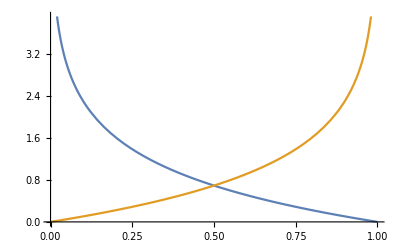

```mathematica
Plot[{L[0,p],L[1,p]},{p,0,1}]
```

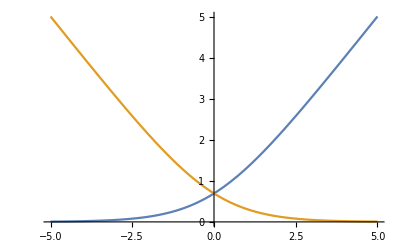

```mathematica
Plot[{L[y,1/(1+Exp[-yh])]/.y->0,L[y,1/(1+Exp[-yh])]/.y->1},{yh,-5,5}]
```

```mathematica
Series[L[y,1/(1+Exp[-yh])],{yh,0,4}]
D[%,yh]
```

Log[2]+1/2 (1-2 y) yh+yh^2/8-yh^4/192+O[yh]^5

1/2 (1-2 y)+yh/4-yh^3/48+O[yh]^4

```mathematica
FullSimplify[Table[D[L[yi,1/(1+Exp[-yh])],{yh,n}]/.yh->yht1,{n,0,4}],Assumptions->{yht1∈Reals}]//MatrixForm
```

(-yht1 yi+Log[1+ⅇ^yht1]
1/(1+ⅇ^-yht1)-yi
ⅇ^yht1/((1+ⅇ^yht1)^2)
-2 Csch[yht1]^3 Sinh[yht1/2]^4
1/8 (-2+Cosh[yht1]) Sech[yht1/2]^4)

```mathematica
Normal[Log[2]+1/2 (1-2 y) yh+yh^2/8-yh^4/192+O[yh]^5]/.y->{1}
```

{-yh/2+yh^2/8-yh^4/192+Log[2]}

```mathematica
Normal[Series[L[y,1/(1+Exp[-yh])],{yh,0,2}]]/.y->{1}
```

{-yh/2+yh^2/8+Log[2]}

```mathematica
Normal[Series[L[y,1/(1+Exp[-yh])],{yh,0,6}]]/.y->1
```

-yh/2+yh^2/8-yh^4/192+yh^6/2880+Log[2]

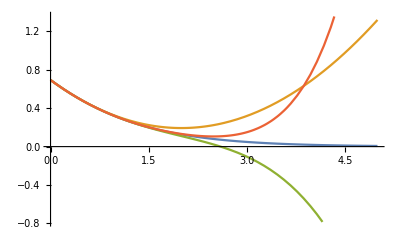

```mathematica
Plot[{L[1,1/(1+Exp[-yh])],-yh/2+yh^2/8+Log[2],-yh/2+yh^2/8-yh^4/192+Log[2],-yh/2+yh^2/8-yh^4/192+yh^6/2880+Log[2]},{yh,0,5}]
```

```mathematica
NMinimize[-yh/2+yh^2/8+Log[2],yh]
NMinimize[-yh/2+yh^2/8-yh^4/192+yh^6/2880+Log[2],yh]
```

{0.193147,{yh→2.}}

{0.105702,{yh→2.48892}}

```mathematica
D[Series[L[y,1/(1+Exp[-yh])],{yh,0,6}],yh]//FullSimplify
```

(1/2-y)+yh/4-yh^3/48+yh^5/480+O[yh]^6

```mathematica
Solve[1/2 (1-2 y)+yh/4-yh^3/48==0,yh]
```

{{yh→-(2 2^(1/3))/((-3+6 y+√(5-36 y+36 y^2))^(1/3))-2^(2/3) (-3+6 y+√(5-36 y+36 y^2))^(1/3)},{yh→(2^(1/3) (1+ⅈ √3))/((-3+6 y+√(5-36 y+36 y^2))^(1/3))+((1-ⅈ √3) (-3+6 y+√(5-36 y+36 y^2))^(1/3))/2^(1/3)},{yh→(2^(1/3) (1-ⅈ √3))/((-3+6 y+√(5-36 y+36 y^2))^(1/3))+((1+ⅈ √3) (-3+6 y+√(5-36 y+36 y^2))^(1/3))/2^(1/3)}}

```mathematica
Solve[1/2 (1-2 y)+yh/4-yh^3/48==0,yh]/.y->{0,1}//N//MatrixForm//Chop
```

(yh→{-2.1038+1.13047 ⅈ,-4.20761}
yh→{4.20761,2.1038-1.13047 ⅈ}
yh→{-2.1038-1.13047 ⅈ,2.1038+1.13047 ⅈ})

```mathematica
1/2 (1-2 y)+yh/4-yh^3/48/.y->{0,1}
```

{1/2+yh/4-yh^3/48,-1/2+yh/4-yh^3/48}

```mathematica
NSolve[1/2+yh/4-yh^3/48==0,yh,Reals]
NSolve[-1/2+yh/4-yh^3/48==0,yh,Reals]
```

{{yh→4.20761}}

{{yh→-4.20761}}

```mathematica
Table[D[(yi-yh)^2,{yh,n}]/.yh->yht1,{n,0,4}]//MatrixForm
```

((-yht1+yi)^2
-2 (-yht1+yi)
2
0
0)

```mathematica
-(1/(1+ⅇ^-yht1)-yi)/(ⅇ^yht1/((1+ⅇ^yht1)^2))//FullSimplify
```

(-1+2 yi) (1+Cosh[yht1])-Sinh[yht1]

```mathematica
(-1+2 yi) (1+Cosh[yht1])-Sinh[yht1]/.yht1->0
```

2 (-1+2 yi)

```mathematica
FullSimplify[Series[L[yi,1/(1+Exp[-yh])],{yh,a,3}],Assumptions->{a>0}]
```

(-a yi+Log[1+ⅇ^a])+(1/(1+ⅇ^-a)-yi) (yh-a)+(yh-a)^2/(4+4 Cosh[a])-1/3 (Csch[a]^3 Sinh[a/2]^4) (yh-a)^3+O[yh-a]^4

```mathematica
FullSimplify[Solve[(1/(1+ⅇ^-yht1)-yi)+(ⅇ^yht1/((1+ⅇ^yht1)^2))x+(-2 Csch[yht1]^3 Sinh[yht1/2]^4)x^2==0,x]]
```

{{x→1/16 Csch[yht1/2]^4 Sinh[yht1]^3 (Sech[yht1/2]^2+√(Sech[yht1/2]^4 (-3+4 Cosh[yht1]+(4-8 yi) Sinh[yht1])))},{x→1/16 Csch[yht1/2]^4 Sinh[yht1]^3 (Sech[yht1/2]^2-√(Sech[yht1/2]^4 (-3+4 Cosh[yht1]+(4-8 yi) Sinh[yht1])))}}